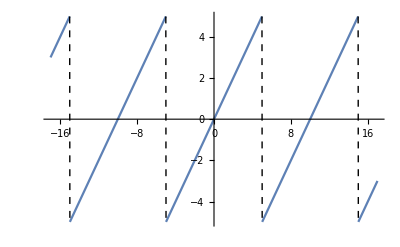

```mathematica
Plot[10 SawtoothWave[(x-5)/10]-5,{x,-17,17},ExclusionsStyle->Dashed]
```

```mathematica
S1 =FourierSeries[t,t,1];
S2 =FourierSeries[t,t,2];
S3 =FourierSeries[t,t,3];
S5 =FourierSeries[t,t,5];
S10 =FourierSeries[t,t,10];
S100 =FourierSeries[t,t,100];
PS1=Plot[{S1,t} ,{t,-π,π}, PlotLegends->Placed[{Subscript["S",1], "f(t)"},Top]];
PS2=Plot[{S2,t} ,{t,-π,π}, PlotLegends->Placed[{Subscript["S",2], "f(t)"},Top]];
PS3=Plot[{S3,t} ,{t,-π,π}, PlotLegends->Placed[{Subscript["S",3], "f(t)"},Top]];
PS5=Plot[{S5,t} ,{t,-π,π}, PlotLegends->Placed[{Subscript["S",5], "f(t)"},Top]];
PS10=Plot[{S10,t} ,{t,-π,π},PlotLegends->Placed[{Subscript["S",10], "f(t)"},Top]];
PS100=Plot[{S100,t} ,{t,-π,π},PlotLegends->Placed[{Subscript["S",100], "f(t)"},Top]];
GraphicsGrid[{{PS1,PS2},{PS3,PS5},{PS10,PS100}}]
```